```mathematica
rf[ϕ_]:=rfamplitude Cos[crest Degree-(ϕ +RandomVariate[NormalDistribution[0,$PhaseResolution]])Degree]
```

```mathematica
qe=QuantityMagnitude[UnitConvert[Quantity["ElectronVolt"]]]
```

1.602177×10^-19

```mathematica
c=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]]
```

299792458

```mathematica
Bρ[p_]:=Evaluate[QuantityMagnitude[UnitConvert[Quantity[p,"eV/c"]/Quantity["ElectronCharge"],"Tesla Meter"]]]
```

```mathematica
dipoleangle[B_,p_:10^6]:=(B dipoleLength)/Bρ[p]
```

```mathematica
finalMomentum[ϕ_]:=If[#<0.1,0.1,#]&[startingP+rf[ϕ]]
```

```mathematica
bpmPosition[B_,ϕ_]:=Block[{finalmom},
finalmom=finalMomentum[ϕ];
If[#<-10,-10,If[#>10,10,#]]&[Mean[Table[10^3(driftLength*(bpmangle-dipoleangle[B,finalmom]))+RandomVariate[NormalDistribution[0,$BPMResolution]],{$BPMAverages}]]]
]
```

## Params

```mathematica
$BPMResolution=0.01;
```

```mathematica
$PhaseResolution=0.25
```

0.25

```mathematica
$BPMAverages=1;
```

```mathematica
crest=167;
```

```mathematica
rfamplitude=20 10^6;
```

```mathematica
dipoleLength=0.2;
```

```mathematica
driftLength=0.2;
```

```mathematica
bpmangle=45Degree;
```

```mathematica
startingP=4.5 10^6;
```

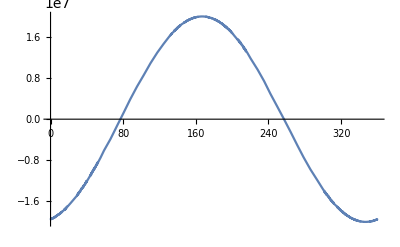

```mathematica
Plot[rf[x],{x,0,360}]
```

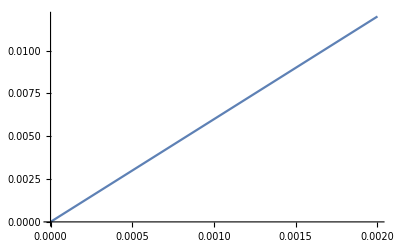

```mathematica
Plot[dipoleangle[B,10 10^6],{B,0,0.002}]
```

```mathematica
bpmPosition[0.3205,crest]
```

0.219336

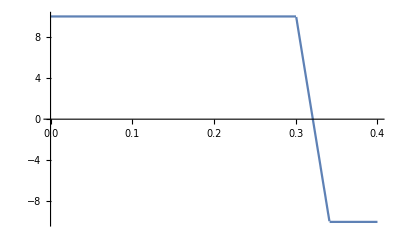

```mathematica
Plot[bpmPosition[B,167],{B,0,0.4}]
```

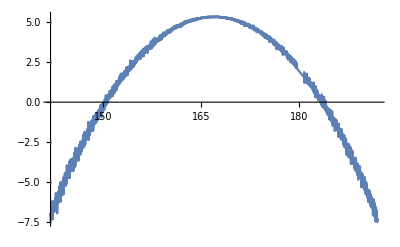

```mathematica
Plot[bpmPosition[0.31,ϕ],{ϕ,crest-25,crest+25}]
```

## Optimiser

```mathematica
findStartingPhase[]:=Block[{bpmpos},
phase=0;
B=0.3;
bpmpos=bpmPosition[B,phase];
While[Not[-10<bpmpos<10],
phase+=1;
bpmpos=bpmPosition[B,phase]
];
phase
]
```

```mathematica
crest
```

167

```mathematica
findStartingPhase[]
```

136

```mathematica
findStartingB[phase_]:=Block[{bpmpos},
B=0.3;
bpmpos=bpmPosition[B,phase];
If[bpmpos>1,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,phase]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,phase]
]];
bpmpos=bpmPosition[B,phase]
]
```

```mathematica
gradient:=Coefficient[Fit[bpmReadings[[-5;;-1]],{1,fitvar},fitvar],fitvar]
```

```mathematica
Clear[optFunc];
optFunc[phase_Real|phase_Integer]:=Block[{bpmpos},
startbpmpos=bpmpos=bpmPosition[B,phase];
If[bpmpos>0,
While[bpmpos>0,
B+=0.001;
bpmpos=bpmPosition[B,phase]
],
While[bpmpos<0,
B-=0.001;
bpmpos=bpmPosition[B,phase]
]
];
offset+=bpmpos-startbpmpos;
AppendTo[bpmReadings,{phase,bpmpos-offset}][[-1,2]]
]
```

```mathematica
Clear[DoOptimisation];
DoOptimisation[startingPhase_]:=Block[{},
phasesign=+1;
offset=0;
bpmReadings={};
phase=findStartingPhase[];
(*findStartingB[phase];*)
(*Print["BPM = ",phase," B = ",B];*)
Do[phase+=2phasesign;optFunc[phase],{5}];
If[gradient<0,phasesign=-phasesign];
(*Print["Gradient = ",gradient];*)
While[phasesign gradient>-1 ,
phase+=√Max[{1Abs[gradient],0.5}] phasesign;
optFunc[phase]
];
guesscrest=Mod[bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]][[1]],360];
{crest-guesscrest,
crest-(ϕ/.FindFit[bpmReadings,{fiteq=a+b Cos[ϕ Degree-x Degree],(guesscrest-20)<ϕ<(guesscrest+20)},{a,b,{ϕ,(guesscrest-20)}},x])}
]
```

```mathematica
$BPMResolution=0.1
```

0.1

```mathematica
$BPMAverages=3
```

3

```mathematica
$PhaseResolution=0.1;
```

```mathematica
crest=RandomReal[{0,360}];
DoOptimisation[startingPhase]
```

{-2.946,-0.244315}

```mathematica
testdata=Table[crest=RandomReal[{0,360}];
DoOptimisation[startingPhase],{500}];
```

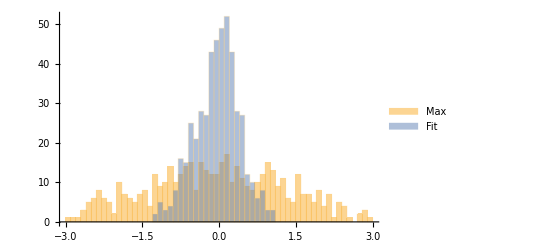

```mathematica
Histogram[Transpose[testdata],{-3,3,0.1},PlotRange->{{-3,3},Automatic},ChartLegends->{"Max","Fit"}]
```

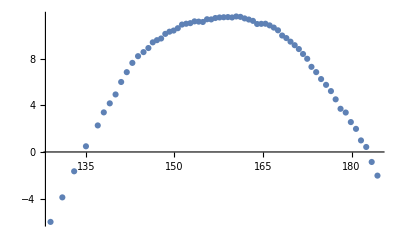

```mathematica
ListPlot[bpmReadings]
```

```mathematica
bpmReadings[[Position[bpmReadings,Max[bpmReadings[[All,2]]]][[1,1]]]]
```

{160.462,11.6001}

```mathematica
Length[bpmReadings]
```

66

```mathematica
(fitans=FindFit[bpmReadings,{fiteq=a+b Cos[ϕ Degree-x Degree]^0.5,0<ϕ<360},{a,b,{ϕ,phase}},x])
```

{a→-252.18,b→263.701,ϕ→143.035}

```mathematica
crest
```

142.799

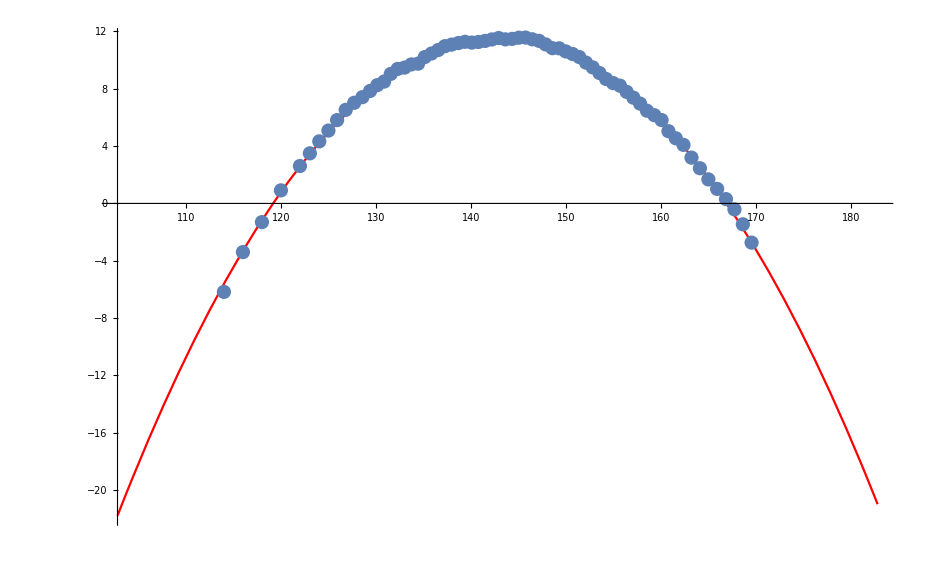

```mathematica
Show[Plot[fiteq/.fitans,{x,crest-40,crest+40},PlotStyle->Red],ListPlot[bpmReadings]]
```

```mathematica
DoOptimisation2[startingPhase_]:=Block[{},
phasesign=+1;
offset=0;
bpmReadings={};
phase=startingPhase;
findStartingB[phase];
Print["BPM = ",phase," B = ",B];
(*Do[phase+=2phasesign;optFunc[phase],{5}];
If[gradient<1,phasesign=-phasesign];
Print["Gradient = ",gradient];*)
FindMaximum[optFunc[p],{{p,phase}}]
]
```

```mathematica
DoOptimisation2[210]
```

BPM = 210 B = -2.70617×10^-16

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{10.,{p→210.}}

```mathematica
bpmReadings
```

{{210.,10},{210.,10},{210.,10}}

```mathematica
optFunc[210]
```

10

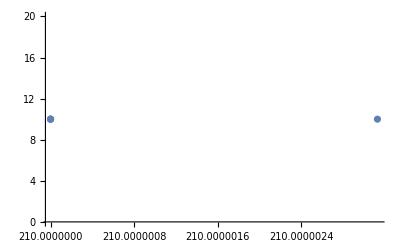

```mathematica
ListPlot[bpmReadings,PlotRange->All]
```